```mathematica
<<peeters`

peeters`setGitDir["../project/figures/phy487-qmsolids"]
```

peeters`

\\wsl$\Ubuntu\home\pjoot\project\figures\phy487-qmsolids

```mathematica
Hybrid orbitals, ps1 q2
```

### verify orthonormality of hybrid orbitals

```mathematica
Clear[psi2s, psi2pz, psi2px, psi2py, rho, phi, theta]
aNought := Subscript[a, 0]
normConst := (z/(2 aNought))^(3/2) / Sqrt[Pi]
rho[r_] := z r /(2 aNought)
psi2s[rho_, phi_, theta_] = normConst E^(-rho) (1 - rho) ;
psi2pz[rho_, phi_, theta_] = normConst E^(-rho) rho Cos[theta] ;
psi2px[rho_, phi_, theta_] = normConst E^(-rho) rho Sin[theta] Cos[phi] ;
psi2py[rho_, phi_, theta_] = normConst E^(-rho) rho Sin[theta] Sin[phi] ;
(* For display *)
{psi2s[ρ, ϕ, θ] ,
psi2pz[ρ, ϕ, θ],
psi2px[ρ, ϕ, θ],
psi2py[ρ, ϕ, θ]} // TraditionalForm
$Assumptions = aNought > 0 && z > 0 ;
```

{(ⅇ^-ρ (1-ρ) (z/a_0)^(3/2))/(2 √(2 π)),(ⅇ^-ρ ρ (z/a_0)^(3/2) cos(θ))/(2 √(2 π)),(ⅇ^-ρ ρ (z/a_0)^(3/2) sin(θ) cos(ϕ))/(2 √(2 π)),(ⅇ^-ρ ρ (z/a_0)^(3/2) sin(θ) sin(ϕ))/(2 √(2 π))}

```mathematica
(*Verify normalization*)
{Integrate[ (psi2s[rho[r], phi, theta])^2 r^2 Sin[theta], {r, 0, Infinity}, {theta, 0, Pi}, {phi, 0, 2 Pi}],
Integrate[ (psi2pz[rho[r], phi, theta])^2 r^2 Sin[theta], {r, 0, Infinity}, {theta, 0, Pi}, {phi, 0, 2 Pi}],
Integrate[ (psi2px[rho[r], phi, theta])^2 r^2 Sin[theta], {r, 0, Infinity}, {theta, 0, Pi}, {phi, 0, 2 Pi}],
Integrate[ (psi2py[rho[r], phi, theta])^2 r^2 Sin[theta], {r, 0, Infinity}, {theta, 0, Pi}, {phi, 0, 2 Pi}]}
```

{1,1,1,1}

```mathematica
(*Verify orthonormality*)
{Integrate[ psi2s[rho[r], phi, theta] psi2px[rho[r], phi, theta] r^2 Sin[theta], {r, 0, Infinity}, {theta, 0, Pi}, {phi, 0, 2 Pi}],
Integrate[ psi2s[rho[r], phi, theta] psi2py[rho[r], phi, theta] r^2 Sin[theta], {r, 0, Infinity}, {theta, 0, Pi}, {phi, 0, 2 Pi}],
Integrate[ psi2s[rho[r], phi, theta] psi2pz[rho[r], phi, theta] r^2 Sin[theta], {r, 0, Infinity}, {theta, 0, Pi}, {phi, 0, 2 Pi}],
Integrate[ psi2px[rho[r], phi, theta] psi2py[rho[r], phi, theta] r^2 Sin[theta], {r, 0, Infinity}, {theta, 0, Pi}, {phi, 0, 2 Pi}],
Integrate[ psi2px[rho[r], phi, theta] psi2pz[rho[r], phi, theta] r^2 Sin[theta], {r, 0, Infinity}, {theta, 0, Pi}, {phi, 0, 2 Pi}],
Integrate[ psi2py[rho[r], phi, theta] psi2pz[rho[r], phi, theta] r^2 Sin[theta], {r, 0, Infinity}, {theta, 0, Pi}, {phi, 0, 2 Pi}]}
```

{0,0,0,0,0,0}

```mathematica
(* Verify integral used in manual verification of 2s normalization *)
(*Integrate[ E^(-a rho) rho^n, {rho, 0, Infinity}]*)
```

### 2b. contour plots of hybrid orbitals at θ = π/2

```mathematica
(* hybrid functions *)
Clear[psi1, psi2, psi3, psi4]
psi1[r_, theta_, phi_] = Sqrt[1/3]psi2s[rho[r], phi, theta] + Sqrt[2/3] psi2px[rho[r], phi, theta] ;
psi2[r_, theta_, phi_] = Sqrt[1/3]psi2s[rho[r], phi, theta] - Sqrt[1/6] psi2px[rho[r], phi, theta] + Sqrt[1/2]psi2py[rho[r], phi, theta] ;
psi3[r_, theta_, phi_] = Sqrt[1/3]psi2s[rho[r], phi, theta] - Sqrt[1/6] psi2px[rho[r], phi, theta] - Sqrt[1/2]psi2py[rho[r], phi, theta] ;
psi4[r_, theta_, phi_] = psi2pz[rho[r], phi, theta] ;

{psi1[r, θ, ϕ] ,
psi2[r, θ, ϕ] ,
psi3[r, θ, ϕ] ,
psi4[r, θ, ϕ] } // TraditionalForm 

(* part b *)
(*Integrate[psi1[r, θ, ϕ]^2 r^2, {r, 0, Infinity}]// Expand// Factor // TraditionalForm*)

Clear[ inner]
(* assume real functions *)

inner[f_, g_] :=Integrate[f[r, theta, phi]g[r, theta, phi] r^2 Sin[theta] ,{r,0,∞}, {theta, 0, Pi}, {phi, 0, 2 Pi}]

Clear[w, x, y, psi1t, psi2t, psi3t, psi4t]
(* Note: z is Z, not z-axis *)

psi1t[x_, y_, z_, theta_] = 
psi1[Sqrt[x^2 + y^2], theta, ArcTan[x, y]]   /. aNought -> 1 ;
psi2t[x_, y_, z_, theta_] = 
psi2[Sqrt[x^2 + y^2], theta, ArcTan[x, y]]  /. aNought -> 1 ;
psi3t[x_, y_, z_, theta_] = 
psi3[Sqrt[x^2 + y^2], theta, ArcTan[x, y]]  /. aNought -> 1 ;
psi4t[x_, y_, z_, theta_] = 
psi4[Sqrt[x^2 + y^2], theta, ArcTan[x, y]]   /. aNought -> 1 ;
```

{(r z (z/a_0)^(3/2) sin(θ) cos(ϕ) ⅇ^(-(r z)/(2 a_0)))/(4 √(3 π) a_0)+((z/a_0)^(3/2) ⅇ^(-(r z)/(2 a_0)) (1-(r z)/(2 a_0)))/(2 √(6 π)),(r z (z/a_0)^(3/2) sin(θ) sin(ϕ) ⅇ^(-(r z)/(2 a_0)))/(8 √π a_0)-(r z (z/a_0)^(3/2) sin(θ) cos(ϕ) ⅇ^(-(r z)/(2 a_0)))/(8 √(3 π) a_0)+((z/a_0)^(3/2) ⅇ^(-(r z)/(2 a_0)) (1-(r z)/(2 a_0)))/(2 √(6 π)),-(r z (z/a_0)^(3/2) sin(θ) sin(ϕ) ⅇ^(-(r z)/(2 a_0)))/(8 √π a_0)-(r z (z/a_0)^(3/2) sin(θ) cos(ϕ) ⅇ^(-(r z)/(2 a_0)))/(8 √(3 π) a_0)+((z/a_0)^(3/2) ⅇ^(-(r z)/(2 a_0)) (1-(r z)/(2 a_0)))/(2 √(6 π)),(r z (z/a_0)^(3/2) cos(θ) ⅇ^(-(r z)/(2 a_0)))/(4 √(2 π) a_0)}

```mathematica
(* Verify orthonormality.  Done by hand on paper in terms of basis functions.  Do here explicitly to verify against typos *)

{inner[psi1, psi1],inner[psi2, psi2],inner[psi3, psi3],inner[psi4, psi4],
inner[psi1, psi2],inner[psi1, psi3],inner[psi1, psi4],
inner[psi2, psi3],inner[psi2, psi4],inner[psi3, psi4]}
```

{1,1,1,1,0,0,0,0,0,0}

```mathematica
Clear[contourPlots]
contourPlots[f_, tInit_]:= Manipulate[
{ContourPlot[ f[u, v, z, theta], {u, -w, w}, {v, -w, w} ,Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"DeepSeaColors"  ],
ContourPlot[ f[u, v, z, theta]^2, {u, -w, w}, {v, -w, w} ,Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"DeepSeaColors"  ],
DensityPlot[ f[u, v, z, theta]^2, {u, -w, w}, {v, -w, w} ,Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"SunsetColors"]}
,{{w, 10, width}, 1, 20,Appearance->"Labeled"}
, {{theta, tInit, θ}, 0, Pi,Appearance->"Labeled"}
,{{z,1, Z}, 1, 20, 1,Appearance->"Labeled"}
]
contourPlots[psi1t, Pi/2]
contourPlots[psi2t, Pi/2]
contourPlots[psi3t, Pi/2]
(* This last plotted with θ = 0 by default, since π/2 is uninteresting for 2 Subscript[p, z]*)
contourPlots[psi4t, 0]
```

### 2d. Interacting orbitals

```mathematica
Clear[psi1reversed, contourPlotsScaled, psi1superposition]
contourPlotsScaled[f_, tInit_]:= Manipulate[
{ContourPlot[ f[u, v, z, theta, s], {u, -w, w + s}, {v, -w, w} ,Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"DeepSeaColors"  ],
ContourPlot[ f[u, v, z, theta, s]^2, {u, -w, w + s}, {v, -w, w} ,Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"DeepSeaColors"  ],
DensityPlot[ f[u, v, z, theta, s]^2, {u, -w, w + s}, {v, -w, w} ,Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"SunsetColors"]}
,{{w, 10, width}, 1, 20,Appearance->"Labeled"}
, {{theta, tInit, θ}, 0, Pi,Appearance->"Labeled"}
,{{z,1, Z}, 1, 20, 1,Appearance->"Labeled"}
, {{s, 2, separation}, 1, 10,Appearance->"Labeled"}
]
psi1reversed[u_, v_, z_, theta_, s_] = psi1t[-u + s, v, z, theta] ;
psi1superposition[u_, v_, z_, theta_, s_] = psi1reversed[u, v, z, theta, s] + psi1t[u, v, z, theta] ;
contourPlotsScaled[ psi1reversed, Pi/2 ]
contourPlotsScaled[ psi1superposition, Pi/2 ]
```

### 3d density/contour plot experimentation ... looks wrong.

```mathematica
(*Clear[f]
f[x_,y_,zz_]=
psi1[Sqrt[x^2 + y^2], ArcSin[zz/Sqrt[x^2 + y^2 + zz^2]], ArcTan[x, y]]^2   /. aNought -> 1 /. z -> 1  ;

(* http://mathematica.stackexchange.com/questions/19575/what-are-the-possible-ways-of-visualizing-a-4d-function-in-mathematica *)
Module[{width, scale, values}, 
width = 10 ;
scale = 0.3 ;
values=Rescale[Table[f[i,j,k],{i,-width,width,scale},{j,-width,width,scale},{k,-4 width,4width,scale/4}]] ;

Image3D[values]
]*)

(* image below isn't what I expected the 3D version to look like.  Did I do something wrong with my translation to cartesian coordinates ? *)
```

```mathematica
(*Clear[p1, p2, p3, p4, p5]
p1 = DynamicModule[{theta=π/2,w=10,z=1},{ContourPlot[psi1t[u,v,z,theta],{u,-w,w},{v,-w,w},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"DeepSeaColors"],ContourPlot[psi1t[u,v,z,theta]^2,{u,-w,w},{v,-w,w},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"DeepSeaColors"],DensityPlot[psi1t[u,v,z,theta]^2,{u,-w,w},{v,-w,w},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"SunsetColors"]}]

p2 = DynamicModule[{theta=π/2,w=10,z=1},{ContourPlot[psi2t[u,v,z,theta],{u,-w,w},{v,-w,w},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"DeepSeaColors"],ContourPlot[psi2t[u,v,z,theta]^2,{u,-w,w},{v,-w,w},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"DeepSeaColors"],DensityPlot[psi2t[u,v,z,theta]^2,{u,-w,w},{v,-w,w},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"SunsetColors"]}]

p3 = DynamicModule[{theta=π/2,w=10,z=1},{ContourPlot[psi3t[u,v,z,theta],{u,-w,w},{v,-w,w},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"DeepSeaColors"],ContourPlot[psi3t[u,v,z,theta]^2,{u,-w,w},{v,-w,w},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"DeepSeaColors"],DensityPlot[psi3t[u,v,z,theta]^2,{u,-w,w},{v,-w,w},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"SunsetColors"]}]

p4 = DynamicModule[{theta=0,w=10,z=1},{ContourPlot[psi4t[u,v,z,theta],{u,-w,w},{v,-w,w},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"DeepSeaColors"],ContourPlot[psi4t[u,v,z,theta]^2,{u,-w,w},{v,-w,w},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"DeepSeaColors"],DensityPlot[psi4t[u,v,z,theta]^2,{u,-w,w},{v,-w,w},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"SunsetColors"]}]

p5 = DynamicModule[{s=2,theta=π/2,w=10,z=1},{ContourPlot[psi1superposition[u,v,z,theta,s],{u,-w,w+s},{v,-w,w},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"DeepSeaColors"],ContourPlot[psi1superposition[u,v,z,theta,s]^2,{u,-w,w+s},{v,-w,w},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"DeepSeaColors"],DensityPlot[psi1superposition[u,v,z,theta,s]^2,{u,-w,w+s},{v,-w,w},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"SunsetColors"]}]*)
```

```mathematica
(*p1 // FullForm*)
```

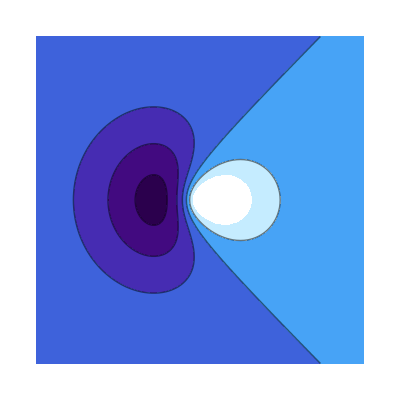
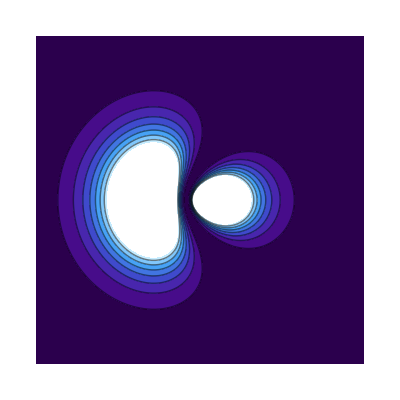
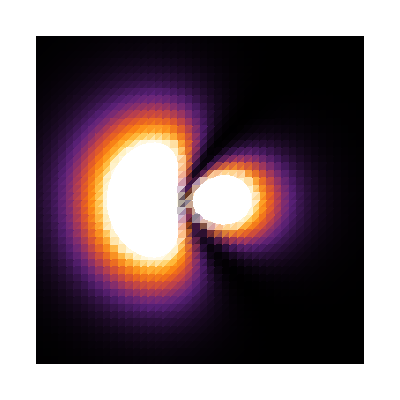
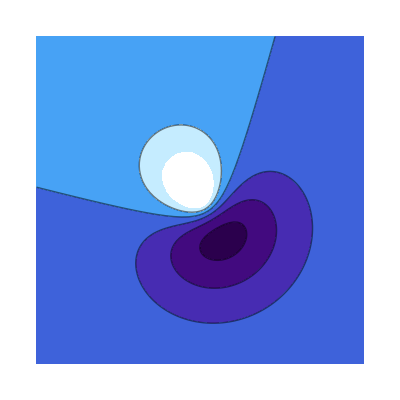
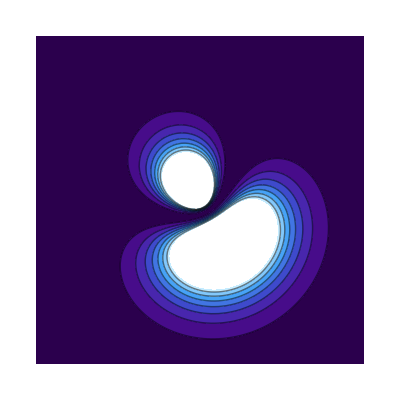
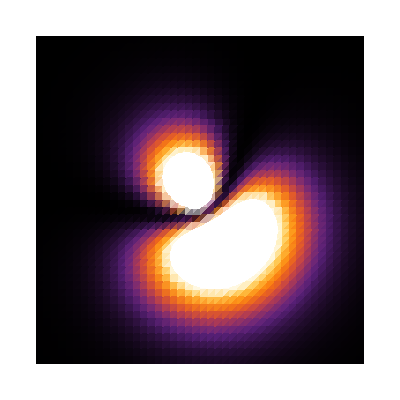
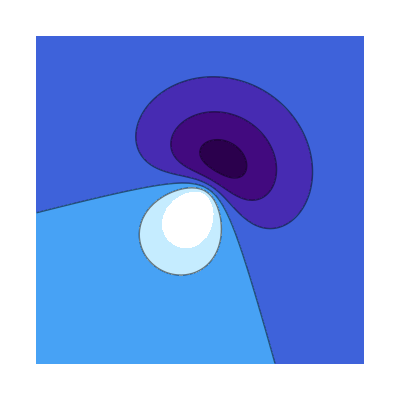
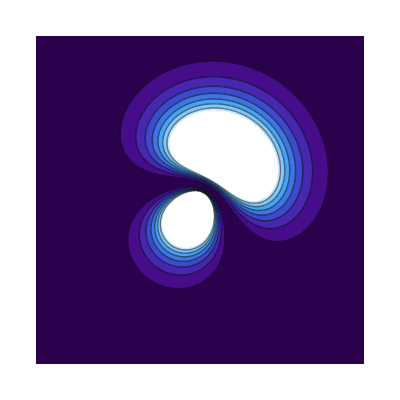

```mathematica
Clear[p]
p={ContourPlot[psi1t[u,v,1,π/2],{u,-10,10},{v,-10,10},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"DeepSeaColors"],ContourPlot[psi1t[u,v,1,π/2]^2,{u,-10,10},{v,-10,10},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"DeepSeaColors"],DensityPlot[psi1t[u,v,1,π/2]^2,{u,-10,10},{v,-10,10},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"SunsetColors"],ContourPlot[psi2t[u,v,1,π/2],{u,-10,10},{v,-10,10},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"DeepSeaColors"],ContourPlot[psi2t[u,v,1,π/2]^2,{u,-10,10},{v,-10,10},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"DeepSeaColors"],DensityPlot[psi2t[u,v,1,π/2]^2,{u,-10,10},{v,-10,10},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"SunsetColors"],ContourPlot[psi3t[u,v,1,π/2],{u,-10,10},{v,-10,10},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"DeepSeaColors"],ContourPlot[psi3t[u,v,1,π/2]^2,{u,-10,10},{v,-10,10},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"DeepSeaColors"],DensityPlot[psi3t[u,v,1,π/2]^2,{u,-10,10},{v,-10,10},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"SunsetColors"],ContourPlot[psi4t[u,v,1,0],{u,-10,10},{v,-10,10},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"DeepSeaColors"],ContourPlot[psi4t[u,v,1,0]^2,{u,-10,10},{v,-10,10},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"DeepSeaColors"],DensityPlot[psi4t[u,v,1,0]^2,{u,-10,10},{v,-10,10},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"SunsetColors"],ContourPlot[psi1superposition[u,v,1,π/2,2],{u,-10,10+2},{v,-10,10},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"DeepSeaColors"],ContourPlot[psi1superposition[u,v,1,π/2,2]^2,{u,-10,10+2},{v,-10,10},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"DeepSeaColors"],DensityPlot[psi1superposition[u,v,1,π/2,2]^2,{u,-10,10+2},{v,-10,10},Mesh->False,Frame->False,PlotPoints->45,ColorFunctionScaling->True,ColorFunction->"SunsetColors"]}
```

```mathematica
(*f[ToString@StringForm["qmSolidPs1OrbitalsPsi1SignedFig``",InputForm[#]], p1[[#]]]  & /@ {1, 2, 3}*)
```

```mathematica
(*<<peeters` ;
setGitDir[ "figures/phy487" ] ;*)
```

```mathematica
peeters`exportForLatex["qmSolidPs1OrbitalsPsi1SignedFig1",p[[1]], True]
peeters`exportForLatex["qmSolidPs1OrbitalsPsi1AbsFig2",p[[2]],True]
peeters`exportForLatex["qmSolidPs1OrbitalsPsi1AbsDensityFig3",p[[3]],True]
peeters`exportForLatex["qmSolidPs1OrbitalsPsi2SignedFig4",p[[4]],True]
peeters`exportForLatex["qmSolidPs1OrbitalsPsi2AbsFig5",p[[5]],True]
peeters`exportForLatex["qmSolidPs1OrbitalsPsi2AbsDensityFig6",p[[6]],True]
peeters`exportForLatex["qmSolidPs1OrbitalsPsi3SignedFig7",p[[7]],True]
peeters`exportForLatex["qmSolidPs1OrbitalsPsi3AbsFig8",p[[8]],True]
peeters`exportForLatex["qmSolidPs1OrbitalsPsi3AbsDensityFig9",p[[9]],True]
peeters`exportForLatex["qmSolidPs1OrbitalsPsi4SignedFig10",p[[10]],True]
peeters`exportForLatex["qmSolidPs1OrbitalsPsi4AbsFig11",p[[11]],True]
peeters`exportForLatex["qmSolidPs1OrbitalsPsi4AbsDensityFig12",p[[12]],True]
peeters`exportForLatex["qmSolidPs1OrbitalsPsi5SignedFig13",p[[13]],True]
peeters`exportForLatex["qmSolidPs1OrbitalsPsi5AbsFig14",p[[14]],True]
peeters`exportForLatex["qmSolidPs1OrbitalsPsi5AbsDensityFig15",p[[15]],True]
```

{C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi1SignedFig1.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi1SignedFig1pn.png}

{C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi1AbsFig2.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi1AbsFig2pn.png}

{C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi1AbsDensityFig3.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi1AbsDensityFig3pn.png}

{C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi2SignedFig4.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi2SignedFig4pn.png}

{C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi2AbsFig5.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi2AbsFig5pn.png}

{C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi2AbsDensityFig6.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi2AbsDensityFig6pn.png}

{C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi3SignedFig7.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi3SignedFig7pn.png}

{C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi3AbsFig8.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi3AbsFig8pn.png}

{C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi3AbsDensityFig9.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi3AbsDensityFig9pn.png}

{C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi4SignedFig10.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi4SignedFig10pn.png}

{C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi4AbsFig11.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi4AbsFig11pn.png}

{C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi4AbsDensityFig12.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi4AbsDensityFig12pn.png}

{C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi5SignedFig13.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi5SignedFig13pn.png}

{C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi5AbsFig14.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi5AbsFig14pn.png}

{C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi5AbsDensityFig15.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\phy487/qmSolidPs1OrbitalsPsi5AbsDensityFig15pn.png}

```mathematica
cover = -Graphics-;
```

cover.jpg

```mathematica
cp[f_, tInit_] := With[{uu = 10,vv=10,theta=tInit, z = 1}, 
DensityPlot[ f[u, v, z, theta]^2, {u, -uu, uu}, {v, -vv, vv} 
,Mesh->False
,Frame->False
,PlotPoints->200
, PlotRange -> All
, PlotRange -> {{-uu,uu},{-vv,vv}}
, AspectRatio->0.8
, ColorFunction-> "SunsetColors"
 ,ImageSize -> 7000
]];

cover = cp[psi1t, Pi/2];

Export["cover"<>".jpg",cover,Background->None]
```

cover.jpg